```mathematica
netMLP=NetChain[{LinearLayer[5],ElementwiseLayer[Tanh],LinearLayer[1]},"Input"->"Scalar","Output"-> "Scalar"]
```

NetChain[<>]

```mathematica
netMLPinit=NetInitialize[netMLP,Method->{"Random","Biases"->2}]
```

NetChain[<>]

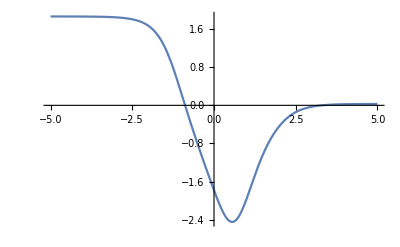

```mathematica
Plot[netMLPinit[x],{x,-5,5}]
```